Week 1 Homework:

### P1 .1 .13 If you invest a dollar at 6% interest compounded monthly , it amounts to (1.005)^(^n) after n months. If you invest $10 at the beginning of each month for 10 years (120 months) how much will you have at the end of 10 years?

We can see this as a geometric series where a=1.005,r=1.005
The formula to find the n-sum is given by S_n=a (1-r^n)/(1-r)
Here, we have n=120 months.
NOTE: The key is that we invest an additional $10 every time, so each sum is multiplied by $10. 
	Also, “a” in this formula represents S_1

```mathematica
10*(1.005*(1-1.005^120)/(1-1.005))
```

1646.99

```mathematica
10*Sum[(1.005)^i,{i,0120}]
```

1646.99

We can apply geometric series to finding definite fractions for certain repeating decimals. 
The formula to find the total sum of the geometric series is by taking the limit:
lim [S_n,n→∞]=a/(1-r)
For example, for 0.55555
	we have a=0.5,r=1/10

```mathematica
1/2/(1-1/10)
```

5/9

### P1 .6 .24 Use the ratio test to determine if ∑_(n=0)^∞ 3^(2 n)/2^(3 n) converges

We can apply the ratio test of doing Limit[(a_(n+1))/a_n,n→∞]

```mathematica
Limit[(3^(2(n+1))/2^(3(n+1)))/(3^(2n)/2^(3n)),n->∞]
```

9/8

### P1 .13 .20 Find the first 3 terms in the Maclaurin series for ⅇ^x Sin[x]. Explicitly generate the sum defined in Eq. 1.12.9 , first by writing out each term. Use /.x->0 to evaluate expressions at zero. Do it again using Sum; you will have to write an expression which evaluates to the nth term. Finally, check your result with Series.

A MacLaurin Series is a Taylor Series evaluated at x_0=0
The formula is given by ∑ _(n=0)^∞ (f^(n)(x_0))/(n!)(x-x_0)^n  
First we define a variable to represent our function:

```mathematica
func=e^x Sin[x]
```

e^x Sin[x]

Explicitly computing the first 3 terms:

```mathematica
a0=(D[func,{x,0}]/.x->0)/(0!)(x-0)^0
```

0

```mathematica
a1=(D[func,{x,1}]/.x->0)/(1!)(x-0)^1
```

x

```mathematica
a2=(D[func,{x,2}]/.x->0)/(2!)(x-0)^2
```

x^2 Log[e]

```mathematica
a3=(D[func,{x,3}]/.x->0)/(3!)(x-0)^3
```

1/6 x^3 (-1+3 Log[e]^2)

Adding all the terms above, we get our MacLaurin Series:

```mathematica
MacSeries=a1+a2+a3
```

x+x^2 Log[e]+1/6 x^3 (-1+3 Log[e]^2)

Now using Sum to compute the MacLaurin Series:

```mathematica
MacSeriesSum=Sum[(D[func,{x,i}]/.x->0)/(i!)(x-0)^i,{i,0,3}]
```

x+x^2 Log[e]+1/6 x^3 (-1+3 Log[e]^2)

Using Series[] to check our answer:

```mathematica
check=Series[func,{x,0,3}]//Normal//Simplify
```

x+x^2 Log[e]+1/6 x^3 (-1+3 Log[e]^2)

```mathematica
MacSeries==MacSeriesSum==check
```

True

### P1 .13 .36 Find the first 3 non-vanishing terms of the Maclaurin series for F[u]=∫_0^u Sin[x]/(√(1-x^2))ⅆx This problem illustrates that you can find the series expansion for an integral, even if you cannot evaluate the integral in closed f,orm.

Defining a variable to represent our function:

```mathematica
func=Integrate[Sin[x]/Sqrt[1-x^2],{x,0,u}]
```

∫_0^u Sin[x]/(√(1-x^2))ⅆx

```mathematica
nterms=6
```

6

Note that the function is in terms of u as the integrals boundaries are from 0→u
Thus we derive the function wrt u and do the power series in terms of u as well.

```mathematica
Sum[(D[func,{u,n}]/.u->0)/(n!)(u-0)^n,{n,0,nterms}]
```

u^2/2+u^4/12+u^6/20

Using Series[] to check our answer

```mathematica
Series[func,{u,0,nterms}]//Normal
```

u^2/2+u^4/12+u^6/20

### P1 .16 .20 Find the first 3 terms of the Taylor’s series of x^(1/3) valid near x=8. Make sure to not include O[x-8] terms in your answer, i.e. put a simple expression into the input field.

```mathematica
func=x^(1/3)
```

x^(1/3)

```mathematica
TaylorFunc[n_]:=(D[func,{x,n}]/.x->8)/(n!)(x-8)^n
```

```mathematica
TSeries=Sum[TaylorFunc[i],{i,0,3}]
```

2+1/12 (-8+x)-1/288 (-8+x)^2+(5 (-8+x)^3)/20736

### P2 .9 .20 Express ((√2)/(ⅈ-1))^10 in x+ ⅈ y ( cartesian) form by expressing the fraction in polar form and then calculating the power. Check by brute force calculation of the power

Defining a variable to represent the given fraction:

```mathematica
ogfrac=Sqrt[2]/(ⅈ-1)
```

-(1+ⅈ)/(√2)

Multiplying our fraction by the complex conjugate to get the denominator to have only real numbers.
Note this is now in Cartesian form, where x=-1/Sqrt[2],y=1/Sqrt[2]

```mathematica
frac=ogfrac*(ⅈ+1)/(ⅈ+1)
```

-(1+ⅈ)/(√2)

Using Abs[] and Arg[] to find the radius and angle of our fraction:

```mathematica
r=Abs[frac]
```

1

```mathematica
θ=Arg[frac]
```

-(3 π)/4

Now that we have the values for r and θ, we can substitute them into Euler’s Formula:

```mathematica
euler=r ⅇ^(ⅈ θ)
```

ⅇ^(-(3 ⅈ π)/4)

The beautiful part of converting into this exponential form is that we can exponentiate the 10 easily.

```mathematica
answer=euler^10
```

ⅈ

We can check our answer just by directly computing the 10th power of the given fraction:

```mathematica
check=(ogfrac)^10
```

ⅈ

### P2 .10 .9 Find all values of 1^(1/5) . Do it first by expressing 1 in polar form and then computing the roots. Check your answer by solving z^5-1=0 and using ComplexExpand. The answer should be a list of the 5 fifth roots.

Like the previous problem, we convert the expression inside the power from Cartesian to Polar Form, then to 
Exponential Form using Euler’s Formula. Once it’s in exponential form, we can find it’s nth-root easily.

```mathematica
cartform=x+y ⅈ/.{x->1,y->0}
```

1

Using Abs[] and Arg[] to find the radius and angle:

```mathematica
r=Abs[cartform]
```

1

```mathematica
θ=Arg[cartform]
```

0

We have to keep in mind that there are infinitely many solutions to obtain this angle. 
Thus we define a general solution to account for any additional multiple of 2π:

```mathematica
θgen=0+2π n
```

2 n π

Then we plug our general θ and our r into the equation r ⅇ^(ⅈ θ), however we take the root by multiplying/dividing
the exponent by whatever root they want:

```mathematica
expform=r^(1/5) ⅇ^(ⅈ θgen/5)
```

ⅇ^((2 ⅈ n π)/5)

```mathematica
ComplexExpand[1^(1/5)ⅇ^(ⅈ 2π/5)]
```

-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)

```mathematica
Solve[z^5-1==0,z]//ComplexExpand
```

{{z→1},{z→-1/4-(√5)/4-ⅈ √(5/8-(√5)/8)},{z→-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)},{z→-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)},{z→-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}}

Then we use Table[] to iterate through each root:

```mathematica
roots=Table[expform,{n,0,4}]//ComplexExpand
```

{1,-1/4+(√5)/4+ⅈ √(5/8+(√5)/8),-1/4-(√5)/4+ⅈ √(5/8-(√5)/8),-1/4-(√5)/4-ⅈ √(5/8-(√5)/8),-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)}

Using Thread[] to put the Table[] results in the format of {Re[Z],Im[Z]} for us to plot:

```mathematica
points=Thread[{Re[roots],Im[roots]}]
```

{{1,0},{-1/4+(√5)/4,√(5/8+(√5)/8)},{-1/4-(√5)/4,√(5/8-(√5)/8)},{-1/4-(√5)/4,-√(5/8-(√5)/8)},{-1/4+(√5)/4,-√(5/8+(√5)/8)}}

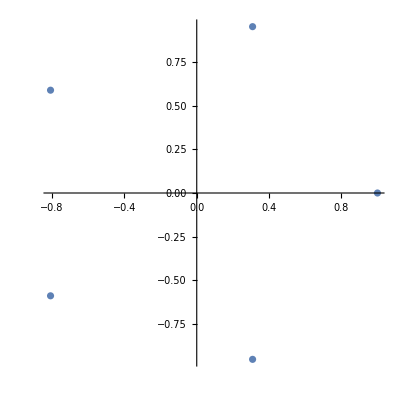

```mathematica
ListPlot[points,AspectRatio->1]
```

### P2 .14 .4 Evaluate Log[ⅈ-1] in x+ ⅈ y (Cartesian) form , first by converting to polar form, and then by using ComplexExpand

```mathematica
eq=-1+ⅈ
```

-1+ⅈ

```mathematica
r=Abs[eq]
```

√2

```mathematica
θ=Arg[eq]
```

(3 π)/4

```mathematica
expform=r ⅇ^(ⅈ θ)
```

√2 ⅇ^((3 ⅈ π)/4)

```mathematica
logform=Log[r]+ⅈ θ
```

(3 ⅈ π)/4+Log[2]/2

```mathematica
check=Log[ⅈ-1]//ComplexExpand
```

(3 ⅈ π)/4+Log[2]/2

Week 2 Homework

### Wk2.P1 Find all of the square roots of ⅈ. Do it by explicitly converting ⅈ into polar form ( with an additional factor of 1=ⅇ^(2π n ⅈ) ) and then evaluating the result. Check using ComplexExpand. Your answer should be a list containing the square roots.

```mathematica
cartform=x+y ⅈ/.{x->0,y->1}
```

ⅈ

```mathematica
r=Abs[cartform]
θ=Arg[cartform]
```

1

π/2

```mathematica
θgen=θ+2π n
```

π/2+2 n π

```mathematica
expform= r^(1/2)ⅇ^(θgen ⅈ /2)
```

ⅇ^(1/2 ⅈ (π/2+2 n π))

```mathematica
roots=Table[expform,{n,0,1}]//ComplexExpand
```

{(1+ⅈ)/(√2),-(1+ⅈ)/(√2)}

```mathematica
points=Thread[{Re[roots],Im[roots]}]
```

{{1/(√2),1/(√2)},{-1/(√2),-1/(√2)}}

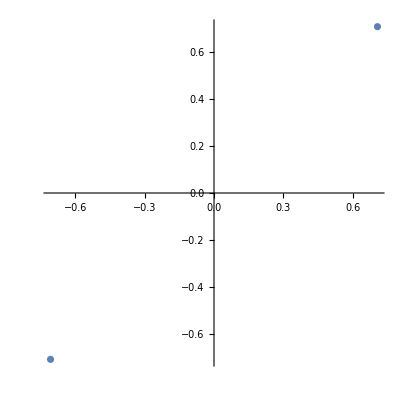

```mathematica
ListPlot[points,AspectRatio->1]
```

### Wk2.P2 Find ⅈ^ⅈ . Do it by explicitly converting each term into polar form and then evaluating the result. Check using ComplexExpand.

```mathematica
cartform=x+y ⅈ/.{x->0,y->1}
```

ⅈ

```mathematica
r=Abs[cartform]
θ=Arg[cartform]
```

1

π/2

```mathematica
expform=r^ⅈ ⅇ^(ⅈ θ ⅈ)
```

ⅇ^(-π/2)

```mathematica
ComplexExpand[ⅈ^ⅈ]
```

ⅇ^(-π/2)

### P2 .17 .26 Find |(2 ⅇ^(ⅈ θ)-ⅈ)/(ⅈ ⅇ^(ⅈ θ)+2)|

```mathematica
Abs[(2 ⅇ^(ⅈ θ)-ⅈ)/(ⅈ ⅇ^(ⅈ θ)+2)]
```

1

### P2 .16 .8 Find the impedance of the circuit in the figure below. A circuit is said to be in resonance if Z is real and ω>0; find the resonant frequency ω_res in terms of R, L, and C ( treating these as symbols, not numbers) . You can use the fact that parallel and series combinations of complex impedances obey the same formulas as parallel and series combinations of resistors. For numerical values R=50 ohms, L=5 milli Henrys and C=0.1 micro Farad, make a plot of Abs[Z] and Arg[Z]

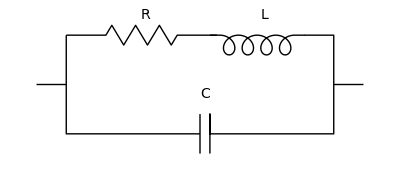

```mathematica
ClearAll["Global`*"]
```

First we define variables to represent the voltage going through the Resistor, Inductor, and Capacitor.
Boas gives the formulas to define each component:

```mathematica
Vr=Res Cur;
Vl=ⅈ ω Ind Cur;
Vc=1/(ⅈ ω Cpct)Cur;
```

Since these are in series, we can just add the voltages of the resistor and the inductor.

```mathematica
Vrl=Vr+Vl//Simplify
```

Cur (Res+ⅈ Ind ω)

We are also given that the complex impedance is: V=Z I, where Z is the complex impedance, I is the current. 

Our next step is to set up these equations and solve for the complex impedances of individual circuit components. 
We can use the given property of parallel and series combinations of complex impedances. 

This equation represents the complex impedance for the resistor and the inductor.

```mathematica
eq1=Vrl==Zrl Cur
```

Cur (Res+ⅈ Ind ω)==Cur Zrl

Solving for Z, we get:

```mathematica
ZsolRL=Solve[eq1,Zrl]//Flatten
```

{Zrl→Res+ⅈ Ind ω}

This equation represents the complex impedance for the capacitance.

```mathematica
eq2=Vc==Zc Cur
```

-(ⅈ Cur)/(Cpct ω)==Cur Zc

Solving for Z, we get:

```mathematica
ZsolC=Solve[eq2,Zc]//Flatten
```

{Zc→-ⅈ/(Cpct ω)}

Now we apply the property of adding complex impedances in series, which is the inverse sum of the inverse impedances.
The total impedance is:

```mathematica
Ztot=(1/Zrl+1/Zc)^-1/.ZsolRL/.ZsolC//Simplify
```

1/(ⅈ Cpct ω+1/(Res+ⅈ Ind ω))

Using ComplexExpand[], we can force our expression into Cartesian form:

```mathematica
ComplexExpand[Ztot]
```

Res/((Res^2+Ind^2 ω^2) (Res^2/((Res^2+Ind^2 ω^2)^2)+(Cpct ω-(Ind ω)/(Res^2+Ind^2 ω^2))^2))+ⅈ (-(Cpct ω)/(Res^2/((Res^2+Ind^2 ω^2)^2)+(Cpct ω-(Ind ω)/(Res^2+Ind^2 ω^2))^2)+(Ind ω)/((Res^2+Ind^2 ω^2) (Res^2/((Res^2+Ind^2 ω^2)^2)+(Cpct ω-(Ind ω)/(Res^2+Ind^2 ω^2))^2)))

The prompt tells us that a circuit is in resonance if Z is real and ω>0
This is equivalent to saying that the imaginary part of Z is zero. 
Thus we can set up another equation that equates Im[Z]=0, and then solve for ω:

```mathematica
ZtotIm=ComplexExpand[Im[Ztot]]
```

-(Cpct ω)/(Res^2/((Res^2+Ind^2 ω^2)^2)+(Cpct ω-(Ind ω)/(Res^2+Ind^2 ω^2))^2)+(Ind ω)/((Res^2+Ind^2 ω^2) (Res^2/((Res^2+Ind^2 ω^2)^2)+(Cpct ω-(Ind ω)/(Res^2+Ind^2 ω^2))^2))

```mathematica
Solve[ZtotIm==0,ω]//Flatten
```

{ω→0,ω→-(√(Ind-Cpct Res^2))/(√Cpct Ind),ω→(√(Ind-Cpct Res^2))/(√Cpct Ind)}

### P3 .5 .24 Find the parametric equation ( of the form r⃗=OverVector[r0]+A⃗ t as in Eq 3.5.8) for the line formed by the intersection of planes defined by 3x+6y-3z=10 and 5x+2y-z=12

```mathematica
n1={3,6,-3}
```

{3,6,-3}

```mathematica
n2={5,2,-1}
```

{5,2,-1}

```mathematica
A=Cross[n1,n2]
```

{0,-12,-24}

```mathematica
eq1=3x+6y-3z==10;
eq2=5x+2y-z==12;
xysol=Solve[{eq1,eq2}/.z->0,{x,y}]//Flatten
```

{x→13/6,y→7/12}

```mathematica
r0={x,y,z}/.z->0/.xysol
```

{13/6,7/12,0}

```mathematica
r=r0+A t
```

{13/6,7/12-12 t,-24 t}

```mathematica
planeplot=ContourPlot3D[{3x+6y-3z==10,5x+2y-z==12},{x,-5,5},{y,-5,5},{z,-5,5}];
lineplot=Graphics3D[{Thickness[0.05],Line[{r/.t->-1,r/.t->0,r/.t->1}]}];
```

```mathematica
Show[planeplot,lineplot]
```

-Graphics3D-

Week 3 Homework

### P3 .5 .32 Find the distance from {3,-1,2} to the plane 5x-y-z=4

Defining a variable to represent the normal vector of the given plane:

```mathematica
n={5,-1,-1}
```

{5,-1,-1}

Defining a variable to represent the given point:

```mathematica
point={3,-1,2}
```

{3,-1,2}

Finding an arbitrary point on the given plane, setting x,y→0:

```mathematica
plane=5x-y-z==4;
```

```mathematica
zsol=Solve[plane/.{x->0,y->0},z]//Flatten
```

{z→-4}

```mathematica
pointonplane={x,y,z}/.{x->0,y->0}/.zsol
```

{0,0,-4}

Finding the vector connecting these two points:

```mathematica
vec=point-pointonplane
```

{3,-1,6}

The distance is given by the scalar projection of our vector and the plane’s normal vector:

```mathematica
distance=(vec.n)/Sqrt[n.n]
```

10/(3 √3)

We can check using the “distance formula” given by: (ax+by+cz+d)/((a^2+b^2+c^2)^(1/2)) where the numerator is our plane equation and 
{x,y,z} are plugged in as the given point:

```mathematica
check=((5x-y-z-4)/.{x->3,y->-1,z->2})/Sqrt[n.n]
```

10/(3 √3)

### P3 .12 .5 Find the equations of 5 x^2+3 y^2+2 z^2+4x z=14 relative to the principal axes. (See Boas 3.12) In the primed principal axis coordinate system, the surface has equation a xp^2+b yp^2+c zp^2=14 ; what are a, b, and c

```mathematica
ClearAll["Global`*"]
```

```mathematica
surface=ContourPlot3D[5 x^2 + 3 y^2 + 2 z^2 + 4 x z == 14,{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-

The given quadratic equation 5 x^2+3 y^2+2 z^2+4x z=14 can be represented in matrix form, the way to do this is
We look at the non-cross terms (x^2,y^2,z^2) and we plug their coefficients in the diagonal entries directly.
The next step is to look at the cross terms (xy,yz,xz) and we plug in their coefficients divided by 2 in the non-diagonal entries. 
For example, if we were given  5 x^2+3 y^2+2 z^2+3xy+6yz+4xz=14 instead
	our matrix would look like (5 | 3 | 2
3/2 | 3 | 3/2
2 | 3 | 2)
For the given equation, the matrix looks like:

```mathematica
mat=({{5, 0, 2}, {0, 3, 0}, {2, 0, 2}})
```

{{5,0,2},{0,3,0},{2,0,2}}

Next step is to find the eigenvectors: 
NOTE: We transpose the result of Eigenvectors[] because we want the columns to be the eigenvectors, not the rows.

```mathematica
U=Eigenvectors[mat]//Transpose
```

{{2,0,-1},{0,1,0},{1,0,2}}

We have to make sure they’re normalized:

```mathematica
U=Map[Normalize,U];
MatrixForm[U]
```

(2/(√5) | 0 | -1/(√5)
0 | 1 | 0
1/(√5) | 0 | 2/(√5))

The reason why we want the eigenvectors is that we’re trying to diagonalize the given matrix:

```mathematica
Ut=Transpose[U];
MatrixForm[Ut]
```

(2/(√5) | 0 | 1/(√5)
0 | 1 | 0
-1/(√5) | 0 | 2/(√5))

Diagonalizing the given matrix, we get:

```mathematica
diag=Ut.mat.U//Simplify;
MatrixForm[diag]
```

(6 | 0 | 0
0 | 3 | 0
0 | 0 | 1)

Multiplying by {xp,yp,zp} on both sides, we get the quadratic form without any cross-terms:

```mathematica
{xp,yp,zp}.diag.{xp,yp,zp}//Simplify
```

{xp,yp,zp}.Umat.{{5,0,2},{0,3,0},{2,0,2}}.tUmat.{xp,yp,zp}

Plotting our new basis:

```mathematica
evec=Eigenvectors[mat]
```

{{2,0,1},{0,1,0},{-1,0,2}}

```mathematica
newbasis={Graphics3D[{Thick,Red,Arrow[{{0,0,0},4evec[[1]]}]}],
Graphics3D[{Thick,Red,Arrow[{{0,0,0},4evec[[2]]}]}],
Graphics3D[{Thick,Red,Arrow[{{0,0,0},4evec[[3]]}]}]};
```

```mathematica
Show[surface,newbasis]
```

-Graphics3D-

### P3 .7 .29 Construct the matrix corresponding to a rotation of 90^∘ about the y axis together with a reflection through the (x,z) plane. Use the standard right handed x̂,ŷ,ẑ basis .

The standard matrix for rotations about the y-axis by θ degrees is given by: 
NOTE: 
	The y-value is preserved whereas the other components are multiplied by combinations of Sin[] and Cos[]
	Also, the determinant is unsurprisingly 1.

```mathematica
rotmat=({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}})
```

{{Cos[θ],0,Sin[θ]},{0,1,0},{-Sin[θ],0,Cos[θ]}}

In this case, we specifically want a 90 degree rotation, so we sub in θ→π/2:

```mathematica
rotmat90=rotmat/.θ->π/2;
MatrixForm[rotmat90]
```

(0 | 0 | 1
0 | 1 | 0
-1 | 0 | 0)

This makes somewhat good sense because our y-value is still being preserved and our x and z values are switched and negated.

Now, we also need a standard matrix that represents reflections through the (x,z) plane.
This means the x-z values are preserved whereas the y-values are reversed (negated):

```mathematica
refmat=({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}})
```

{{1,0,0},{0,-1,0},{0,0,1}}

The composite matrix corresponding to several transformations is simply the product of the individual standard matrices:

```mathematica
finalmat=rotmat90.refmat;
MatrixForm[finalmat]
```

(0 | 0 | 1
0 | -1 | 0
-1 | 0 | 0)

### Wk3.P2 Consider the vector space of cubic polynomials with basis {1,x,x^2,x^3} . Let T be the operator that returns x p’[x] for any polynomial p[x] . What is the matrix representation of T in this basis?

We can see that T resembles the differentiation operator, however, it has an additional multiple of x in the end. 
We can deduce the matrix representation of T by examining its effects on the basis vectors, in this case our basis is {1,x,x^2,x^3}:

For the basis of 1, we get:

```mathematica
basis1=1;
D[basis1,x]*x
```

0

This is what the first column of our standard matrix looks like.

For the basis of x, we get:

```mathematica
basisx=x;
D[basisx,x]*x
```

x

This is what the second column of our standard matrix looks like.

For x^2, we get:

```mathematica
basisx2=x^2;
D[basisx2,x]*x
```

2 x^2

This is what the third column of our standard matrix looks like.

For x^3, we get:

```mathematica
basisx3=x^3;
D[basisx3,x]*x
```

3 x^3

This is what the fourth column of our standard matrix looks like.
Putting all the columns together, we get:

```mathematica
col1={0,0,0,0};
col2={0,1,0,0};
col3={0,0,2,0};
col4={0,0,0,3};
```

```mathematica
mat={col1,col2,col3,col4};
MatrixForm[mat]
```

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 3)

### Wk3.P3 Verify that (3 | 1+ⅈ | ⅈ 1-ⅈ | 1 | 3 -ⅈ | 3 | 1) is Hermitian. Find a unitary matrix which will diagonalize it via a similarity transformation. Use N to get numerical values. Use Chop ( look it up) to get rid of roundoff error.

Defining a variable to represent the given matrix:

```mathematica
Hmat=({{3, 1+ⅈ, ⅈ}, {1-ⅈ, 1, 3}, {-ⅈ, 3, 1}})
```

{{3,1+ⅈ,ⅈ},{1-ⅈ,1,3},{-ⅈ,3,1}}

We can verify that the given matrix is Hermitian by equating it to its conjugate transpose:

```mathematica
Hmatct=ConjugateTranspose[Hmat];
MatrixForm[Hmatct]
```

(3 | 1+ⅈ | ⅈ
1-ⅈ | 1 | 3
-ⅈ | 3 | 1)

And we do see that this matrix is Hermitian:

```mathematica
Hmatct==Hmat
```

True

We can also verify that the matrix is Hermitian by equating its transpose and its conjugate:

```mathematica
Conjugate[Hmat]==Transpose[Hmat]
```

True

```mathematica
U=Map[Normalize,Eigenvectors[Hmat]]//Transpose//N//Chop;
MatrixForm[U]
```

(0.230473+0.551826 ⅈ | 0.148661-0.005275 ⅈ | -0.478368-0.625625 ⅈ
0.579937+0.0768244 ⅈ | -0.709578+0.0495538 ⅈ | 0.355511-0.159456 ⅈ
0.547851 | 0.686961 | 0.477435)

```mathematica
Uct=ConjugateTranspose[U]//Chop;
MatrixForm[Uct]
```

(0.230473-0.551826 ⅈ | 0.579937-0.0768244 ⅈ | 0.547851
0.148661+0.005275 ⅈ | -0.709578-0.0495538 ⅈ | 0.686961
-0.478368+0.625625 ⅈ | 0.355511+0.159456 ⅈ | 0.477435)

```mathematica
diag=Uct.Hmat.U//Chop;
MatrixForm[diag]
```

(5.18296 | 0 | 0
0 | -2.10645 | 0
0 | 0 | 1.92349)

### Diagonalization Example:

Defining the given matrix:

```mathematica
mat={{4,-3,-3},{3,-2,-3},{-1,1,2}};
MatrixForm[mat]
```

(4 | -3 | -3
3 | -2 | -3
-1 | 1 | 2)

Using Eigenvectors[] and Transpose[] to generate a matrix U whose columns are the eigenvectors of the given matrix:

```mathematica
U=Eigenvectors[mat]//Transpose;
MatrixForm[U]
```

(-3 | 1 | 1
-3 | 0 | 1
1 | 1 | 0)

Using Inverse[] to find the inverse of the given matrix:

```mathematica
Ut=Inverse[U];
MatrixForm[Ut]
```

(-1 | 1 | 1
1 | -1 | 0
-3 | 4 | 3)

Applying the diagonalization formula: D=U^-1 M U

```mathematica
diag=Ut.mat.U;
MatrixForm[%]
```

(2 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

The entries of our new diagonal matrix ought to match the eigenvalues of the given matrix:

```mathematica
Eigenvalues[mat]
```

{2,1,1}

We can apply the reverse of the formula to obtain original matrix by doing M=U D U^-1

```mathematica
ogmat=U.diag.Ut;
MatrixForm[ogmat]
```

(4 | -3 | -3
3 | -2 | -3
-1 | 1 | 2)

We see that the diagonalization formula: D=U^-1 M U works for D is a diagonal matrix and M is a “diagonalizable” matrix.

Week 4 Homework:

### P3 .12 .16 Find the characteristic frequencies and characteristic modes of vibration for the system of masses and springs as shown in the figure.

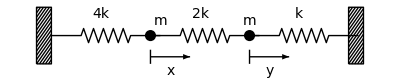

This is our expression of the potential energy with time dependence on x and y:

```mathematica
pot=(1/2 Subscript[k, 1] x[t]^2+1/2 Subscript[k, 2](-x[t]+y[t])^2+1/2 Subscript[k, 3] y[t]^2)/.{Subscript[k, 1]->4k,Subscript[k, 2]->2k,Subscript[k, 3]->1k}
```

2 k x[t]^2+1/2 k y[t]^2+k (-x[t]+y[t])^2

To write the equations of motion, we take the negative derivative for the potential energy with respect to distance.
The motion in x is:

```mathematica
xmot=m x''[t]==Simplify[-D[pot,x[t]]]
```

m x''[t]==2 k (-3 x[t]+y[t])

The motion in y is:

```mathematica
ymot=m y''[t]==Simplify[-D[pot,y[t]]]
```

m y''[t]==k (2 x[t]-3 y[t])

We can put these equations of motion in a list:

```mathematica
eqmot={xmot,ymot}//Expand;
TableForm[eqmot]
```

m x''[t]==-6 k x[t]+2 k y[t]
m y''[t]==2 k x[t]-3 k y[t]

We can confirm if these are the right equations by intuitively creating the force equations ourselves:

```mathematica
xmotguess=m x''[t]==(-Subscript[k, 1]x[t]-Subscript[k, 2] x[t]+Subscript[k, 2] y[t])/.{Subscript[k, 1]->4k,Subscript[k, 2]->2k,Subscript[k, 3]->1k}
```

m x''[t]==-6 k x[t]+2 k y[t]

```mathematica
ymotguess=m y''[t]==(Subscript[k, 2] x[t]-Subscript[k, 2] y[t]-Subscript[k, 3] y[t])/.{Subscript[k, 1]->4k,Subscript[k, 2]->2k,Subscript[k, 3]->1k}
```

m y''[t]==2 k x[t]-3 k y[t]

Above, we do see that our guess matches the derivative of the potential energy. We generated these guesses
by focusing on just one mass, then seeing the direction and magnitude of each spring force (F=±k x) where
x is just the displacement of either mass. 

Plugging in periodic solutions for x[t] and y[t] with the same time dependence, but different amplitudes.
In this case, we are asked for our trial solutions to assume the form of ⅇ^(ⅈ ω t):

```mathematica
eqmot2=eqmot/.{x->Function[t,Ax ⅇ^(ⅈ ω t)],y->Function[t,Ay ⅇ^(ⅈ ω t)]};
TableForm[eqmot2]
```

-Ax ⅇ^(ⅈ t ω) m ω^2==-6 Ax ⅇ^(ⅈ t ω) k+2 Ay ⅇ^(ⅈ t ω) k
-Ay ⅇ^(ⅈ t ω) m ω^2==2 Ax ⅇ^(ⅈ t ω) k-3 Ay ⅇ^(ⅈ t ω) k

We can clean up these equations a little bit by doing the substitution t→0:

```mathematica
eqmot3=eqmot2/.t->0;
TableForm[eqmot3]
```

-Ax m ω^2==-6 Ax k+2 Ay k
-Ay m ω^2==2 Ax k-3 Ay k

In order to solve for ω, we can generate a coefficient matrix for Ax and Ay. 
We can rewrite the above two equations in matrix form: 
m ω^2(Ax
Ay)=(6k | -2k
-2k | 3k)(Ax
Ay)
Moving the left side to the right side:
(6k | -2k
-2k | 3k)(Ax
Ay)-m ω^2(Ax
Ay)=0
Simplifying:
(6k-m ω^2 | -2k
-2k | 3k-m ω^2)(Ax
Ay)=0
Defining a variable to represent our coefficient matrix:

```mathematica
mat={{6k-m ω^2,-2k},{-2k,3k-m ω^2}};
MatrixForm[mat]
```

(6 k-m ω^2 | -2 k
-2 k | 3 k-m ω^2)

Solving for the eigenvalues, we get:

```mathematica
efreq=Solve[Det[mat]==0,ω]
```

{{ω→-(√2 √k)/(√m)},{ω→(√2 √k)/(√m)},{ω→-(√7 √k)/(√m)},{ω→(√7 √k)/(√m)}}

The positive values are the characteristic frequency of vibration. Each frequency is associated with a mode of vibration, 
which can be found by its null space or eigenvector:

```mathematica
NullSpace[mat/.ω->(√2 √k)/(√m)]
```

{{1/2,1}}

```mathematica
NullSpace[mat/.ω->(√7 √k)/(√m)]
```

{{-2,1}}

We can see that for the first mode of vibration, they go in the same direction ie both positive. However, for the 
second mode of vibration, they both go in opposite direction ie opposite signs

### P3 .12 .18 Find the characteristic frequencies and characteristic modes of vibration for the system of masses and springs as shown in the figure.

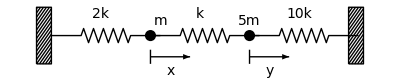

Writing our potential energy equation:

```mathematica
pot=(1/2 Subscript[k, 1] x[t]^2+1/2 Subscript[k, 2](-x[t]+y[t])^2+1/2 Subscript[k, 3] y[t]^2)/.{Subscript[k, 1]->2k,Subscript[k, 2]->1k,Subscript[k, 3]->10k}
```

k x[t]^2+5 k y[t]^2+1/2 k (-x[t]+y[t])^2

Generating equations of motion for x and y by taking the negative derivative of the potential energy
with respect to distance:

```mathematica
xmot=m x''[t]==-D[pot,x[t]]//Expand
```

m x''[t]==-3 k x[t]+k y[t]

```mathematica
ymot=5m y''[t]==-D[pot,y[t]]//Expand
```

5 m y''[t]==k x[t]-11 k y[t]

```mathematica
eqmot={xmot,ymot};
TableForm[eqmot]
```

m x''[t]==-3 k x[t]+k y[t]
5 m y''[t]==k x[t]-11 k y[t]

Plugging in our trial solution for x[t] and y[t] in the form of A ⅇ^(ⅈ ω t):

```mathematica
eqmot2=eqmot/.{x->Function[t,Ax ⅇ^(ⅈ ω t)],y->Function[t,Ay ⅇ^(ⅈ ω t)]};
TableForm[eqmot2]
```

-Ax ⅇ^(ⅈ t ω) m ω^2==-3 Ax ⅇ^(ⅈ t ω) k+Ay ⅇ^(ⅈ t ω) k
-5 Ay ⅇ^(ⅈ t ω) m ω^2==Ax ⅇ^(ⅈ t ω) k-11 Ay ⅇ^(ⅈ t ω) k

We clean up our equation by subbing in t→0

```mathematica
eqmot3=eqmot2/.t->0;
TableForm[eqmot3]
```

-Ax m ω^2==-3 Ax k+Ay k
-5 Ay m ω^2==Ax k-11 Ay k

Rewriting the above equations in matrix form: 
(m ω^2 | 0
0 | 5m ω^2)(Ax
Ay)=(3k | -k
-k | 11k)(Ax
Ay)
Moving everything onto one side: 
(3k | -k
-k | 11)(Ax
Ay)-(m ω^2 | 0
0 | 5m ω^2)(Ax
Ay)=0
Simplifying: 
(3k-m ω^2 | -k
-k | 11k-5m ω^2)(Ax
Ay)=0
Our coefficient matrix now looks like:

```mathematica
mat={{3k-m ω^2,-k},{-k,11k-5m ω^2}};
MatrixForm[mat]
```

(3 k-m ω^2 | -k
-k | 11 k-5 m ω^2)

It’s characteristic frequency is given by its eigenvalues:

```mathematica
Solve[Det[mat]==0,ω]//Simplify
```

{{ω→-(√2 √k)/(√m)},{ω→(√2 √k)/(√m)},{ω→-(4 √k)/(√5 √m)},{ω→(4 √k)/(√5 √m)}}

The characteristic modes are given by its eigenvectors:

```mathematica
NullSpace[mat/.ω->(√2 √k)/(√m)]
```

{{1,1}}

```mathematica
NullSpace[mat/.ω->(4 √k)/(√5 √m)]
```

{{-5,1}}

### P3 .15 .18 Find the matrix C that diagonalizes M=(1 | 0 3 | -2) . Observe that M is not symmetric and C is not orthogonal. However C does have an inverse C^-1 ; find C^-1 and show C^-1M C=D

Defining a variable to represent the given matrix:

```mathematica
mat={{1,0},{3,-2}};
MatrixForm[mat]
```

(1 | 0
3 | -2)

C is the standard matrix used to diagonalize the given matrix M. 
We can construct C by having its columns be the eigenvectors of M:

```mathematica
Cmat=Eigenvectors[mat]//Transpose;
MatrixForm[Cmat]
```

(0 | 1
1 | 1)

Using Inverse[] to find its inverse:

```mathematica
invCmat=Inverse[Cmat];
MatrixForm[invCmat]
```

(-1 | 1
1 | 0)

Applying the diagonalization formula:

```mathematica
diag=invCmat.mat.Cmat;
MatrixForm[diag]
```

(-2 | 0
0 | 1)

We can see from earlier that because M is not symmetric, it’s matrix C is not orthogonal. If C were orthogonal then it’s inverse
would be the transpose. Furthermore, the formula to diagonalize becomes: D=C^-1 M C=C^T M C

### PWk4 .1 Define an inner product <f,g>= ∫_0^∞ ⅇ^-t f[t] g[t]ⅆt . Consider the functions {1,t,t^2,t^3,t^4} . Apply the Gram-Schmidt process to construct an orthonormal set of functions. Verify that they are orthonormal by constructing a table of all of the inner products . Do not use Orthogonalize ( you can use it to check your answer) , but work out conditions for each e[i] .

```mathematica
ClearAll["Global`*"]
```

We can start by defining our given basis:

```mathematica
Thread[{old[1],old[2],old[3],old[4],old[5]}={1,t,t^2,t^3,t^4}]
```

{1,t,t^2,t^3,t^4}

Symbolically, our new orthonormal basis vectors will look like:

```mathematica
Table[e[i],{i,1,5}]
```

{e[1],e[2],e[3],e[4],e[5]}

Defining our inner product function:

```mathematica
inner[f_,g_]:=Integrate[ⅇ^-t f*g,{t,0,∞}]
```

The first orthonormal vector of our new basis can just assume the first vector of our old basis:

```mathematica
e[1]=old[1]/Sqrt[inner[old[1],old[1]]]
```

1

We can define the second new basis vector as some linear combination of the first 2 old basis vectors:

```mathematica
e[2]=a old[1]+b old[2]
```

a+b t

where a and b are just constants.

Now we have a simple, symbolic expression for our new basis. We can generate conditions based on orthonormal properties that we know ought to be true, turn these conditions into equation form, and use Solve[] to find solutions to the constants (a,b):

```mathematica
cond1=inner[e[2],e[2]]==1
```

a^2+2 a b+2 b^2==1

```mathematica
cond2=inner[e[2],e[1]]==0
```

a+b==0

Cond1 is the normalized condition and Cond2 is the orthogonal condition. 
Nonetheless, 2 equations and 2 unknowns, we can solve this bitch:

```mathematica
sol1=Solve[{cond1,cond2},{a,b}]//First
```

{a→-1,b→1}

We can post-wrap //First[] on the solution just to arbitrarily select only one of the given solutions.
Subbing in these solutions, our second new basis vector is:

```mathematica
e[2]=e[2]/.sol1
```

-1+t

Moving onto the next new basis vector, we can write it as a linear combination of the first 3 old basis vectors:

```mathematica
e[3]=a old[1]+b old[2]+c old[3]
```

a+b t+c t^2

Notice that we will always have the 1 condition concerning normalization, and n-1 conditions concerning orthogonality. 
For instance, for the third new basis vector, it ought obey the normalization property and it ought to be orthogonal
to the first and second new basis vectors:

```mathematica
cond1=inner[e[3],e[3]]==1
```

a^2+2 a b+2 b^2+4 (a+3 b) c+24 c^2==1

```mathematica
cond2=inner[e[3],e[2]]==0
```

b+4 c==0

```mathematica
cond3=inner[e[3],e[1]]==0
```

a+b+2 c==0

```mathematica
sol2=Solve[{cond1,cond2,cond3},{a,b,c}]//First
```

{a→1,b→-2,c→1/2}

```mathematica
e[3]=e[3]/.sol2
```

1-2 t+t^2/2

Rinse & repeat. 
We define our fourth new basis vector:

```mathematica
e[4]=a old[1]+b old[2]+c old[3]+d old[4]
```

a+b t+c t^2+d t^3

```mathematica
cond1=inner[e[4],e[4]]==1
```

a^2+2 a (b+2 c+6 d)+2 (b^2+6 b (c+4 d)+12 (c^2+10 c d+30 d^2))==1

```mathematica
cond2=inner[e[4],e[3]]==0
```

2 (c+9 d)==0

```mathematica
cond3=inner[e[4],e[2]]==0
```

b+4 c+18 d==0

```mathematica
cond4=inner[e[4],e[1]]==0
```

a+b+2 c+6 d==0

```mathematica
sol3=Solve[{cond1,cond2,cond3,cond4},{a,b,c,d}]//First
```

{a→-1,b→3,c→-3/2,d→1/6}

```mathematica
e[4]=e[4]/.sol3
```

-1+3 t-(3 t^2)/2+t^3/6

Rinse & repeat
We define our fifth new basis vector:

```mathematica
e[5]=a old[1]+b old[2]+c old[3]+d old[4]+e old[5]
```

a+b t+c t^2+d t^3+e t^4

```mathematica
cond1=inner[e[5],e[5]]==1
```

a^2+2 a (b+2 c+6 d+24 e)+2 (b^2+6 b (c+4 (d+5 e))+12 (c^2+10 c (d+6 e)+30 (d^2+14 d e+56 e^2)))==1

```mathematica
cond2=inner[e[5],e[4]]==0
```

6 (d+16 e)==0

```mathematica
cond3=inner[e[5],e[3]]==0
```

2 (c+9 (d+8 e))==0

```mathematica
cond4=inner[e[5],e[2]]==0
```

b+4 c+18 d+96 e==0

```mathematica
cond5=inner[e[5],e[1]]==0
```

a+b+2 c+6 d+24 e==0

```mathematica
sol4=Solve[{cond1,cond2,cond3,cond4,cond5},{a,b,c,d,e}]//First
```

{a→1,b→-4,c→3,d→-2/3,e→1/24}

```mathematica
e[5]=e[5]/.sol4
```

1-4 t+3 t^2-(2 t^3)/3+t^4/24

This is quite tiresome. Now we’ve found all the coefficients to numerically define our new basis. 
Our new basis looks like:

```mathematica
Thread[{new[1],new[2],new[3],new[4],new[5]}={e[1],e[2],e[3],e[4],e[5]}]//Simplify
```

{1,-1+t,1/2 (2-4 t+t^2),1/6 (-6+18 t-9 t^2+t^3),1-4 t+3 t^2-(2 t^3)/3+t^4/24}

We can check our answer using Orthogonalize[]:

```mathematica
check=Orthogonalize[{old[1],old[2],old[3],old[4],old[5]},inner]//Simplify
```

{1,-1+t,1/2 (2-4 t+t^2),1/6 (-6+18 t-9 t^2+t^3),1-4 t+3 t^2-(2 t^3)/3+t^4/24}

```mathematica
Table[inner[new[i],new[j]],{i,1,5},{j,1,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

### P7 .5 .5 f(x) =0 | ,-π<x<0 -1 | ,0<x<π/2 0 | π/2<x<π is periodic with period 2 π . Construct the Fourier sine-cosine series ( first 5 or so terms for each function) and plot f(x) and the Fourier series approximation . I used Mod[x,2π,-π] ( look it up) to make a function periodic over the interval -π,π.

First, plotting our function using Which[]:

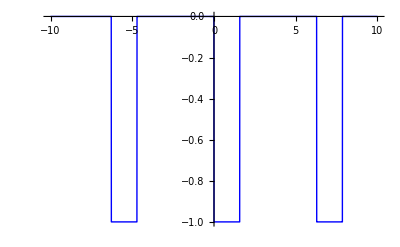

```mathematica
func=Which[-π<Mod[x,2π,-π]<0,0,0<Mod[x,2π,-π]<π/2,-1,π/2<Mod[x,2π,-π]<π,0];
funcplot=Plot[func,{x,-10,10},Exclusions->None,PlotStyle->{Blue,Thick}]
```

We can symbolically define our Fourier Series. We will adopt the linear combinations of A[n] Sin[n x] and B[n] Cos[n x]
where A[n],B[n] are the coefficients.

```mathematica
nterms=10
```

10

```mathematica
fourser=Sum[A[i] Sin[i x]+B[i]Cos[i x],{i,0,nterms}]
```

B[0]+B[1] Cos[x]+B[2] Cos[2 x]+B[3] Cos[3 x]+B[4] Cos[4 x]+B[5] Cos[5 x]+B[6] Cos[6 x]+B[7] Cos[7 x]+B[8] Cos[8 x]+B[9] Cos[9 x]+B[10] Cos[10 x]+A[1] Sin[x]+A[2] Sin[2 x]+A[3] Sin[3 x]+A[4] Sin[4 x]+A[5] Sin[5 x]+A[6] Sin[6 x]+A[7] Sin[7 x]+A[8] Sin[8 x]+A[9] Sin[9 x]+A[10] Sin[10 x]

We can now define 4 functions to represent the left-hand side and right-hand side of the equation after we take the inner
product of both sides and then integrate.
NOTE: 	This is unlike how we usually define just the 2 functions because we are doing a basis of both Sin[] and Cos[] so we need
		2 functions for each basis. 
		Also keep in mind of orthogonality, we must confirm that whatever’s inside the Sin[] and Cos[] ought to match our
		symbolic Fourier Series

```mathematica
sinlhs[n_]:=Integrate[func Sin[n x],{x,-π,π}]
sinrhs[n_]:=Integrate[fourser Sin[n x],{x,-π,π}]
```

Now for the Cos[] basis:

```mathematica
coslhs[n_]:=Integrate[func Cos[n x],{x,-π,π}]
cosrhs[n_]:=Integrate[fourser Cos[n x],{x,-π,π}]
```

Now we use Table[] to create a list of a bunch of equations that we can use to solve for the coefficients. 
We can do them individually, Sin[] and Cos[], then use Join[] to combine the 2 lists of equations.

```mathematica
sineqs=Table[sinlhs[i]==sinrhs[i],{i,0,nterms}];
TableForm[sineqs]
```

True
-1==π A[1]
-1==π A[2]
-1/3==π A[3]
0==π A[4]
-1/5==π A[5]
-1/3==π A[6]
-1/7==π A[7]
0==π A[8]
-1/9==π A[9]
-1/5==π A[10]

```mathematica
coseqs=Table[coslhs[i]==cosrhs[i],{i,0,nterms}];
TableForm[coseqs]
```

-π/2==2 π B[0]
-1==π B[1]
0==π B[2]
1/3==π B[3]
0==π B[4]
-1/5==π B[5]
0==π B[6]
1/7==π B[7]
0==π B[8]
-1/9==π B[9]
0==π B[10]

Solving for both coefficients A[n] and B[n]:

```mathematica
sol=Solve[Join[sineqs,coseqs],Join[Table[A[i],{i,1,nterms}],Table[B[i],{i,0,nterms}]]]//Flatten
```

{A[1]→-1/π,A[2]→-1/π,A[3]→-1/(3 π),A[4]→0,A[5]→-1/(5 π),A[6]→-1/(3 π),A[7]→-1/(7 π),A[8]→0,A[9]→-1/(9 π),A[10]→-1/(5 π),B[0]→-1/4,B[1]→-1/π,B[2]→0,B[3]→1/(3 π),B[4]→0,B[5]→-1/(5 π),B[6]→0,B[7]→1/(7 π),B[8]→0,B[9]→-1/(9 π),B[10]→0}

Plugging in our solution:

```mathematica
fourser2=fourser/.sol
```

-1/4-Cos[x]/π+Cos[3 x]/(3 π)-Cos[5 x]/(5 π)+Cos[7 x]/(7 π)-Cos[9 x]/(9 π)-Sin[x]/π-Sin[2 x]/π-Sin[3 x]/(3 π)-Sin[5 x]/(5 π)-Sin[6 x]/(3 π)-Sin[7 x]/(7 π)-Sin[9 x]/(9 π)-Sin[10 x]/(5 π)

Plotting our given function and our Fourier Series:

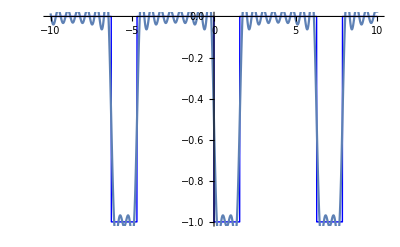

```mathematica
fourplot=Plot[fourser2,{x,-10,10}];
Show[funcplot,fourplot]
```

Week 5 Homework:

### P7 .5 .11 Consider the periodic function f[x] = 0 | -π<x<0 Sin[x] | 0<x<π Make a plot of the function. Find the Fourier series for the function using any convenient tools, and make a plot that shows the comparison.

We can start off by defining the given function:

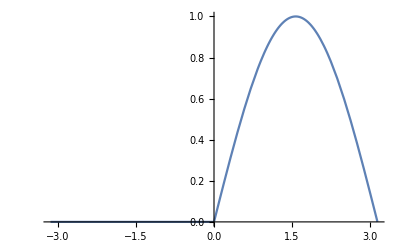

```mathematica
func=Which[-π<x<0,0,0<x<π,Sin[x]];
Plot[func,{x,-π,π}]
```

```mathematica
fourser=FourierSeries[func,x,5]
```

1/4 ⅈ ⅇ^(-ⅈ x)-1/4 ⅈ ⅇ^(ⅈ x)+1/π-ⅇ^(-2 ⅈ x)/(3 π)-ⅇ^(2 ⅈ x)/(3 π)-ⅇ^(-4 ⅈ x)/(15 π)-ⅇ^(4 ⅈ x)/(15 π)

```mathematica
fourtrig=ExpToTrig[fourser]
```

1/π-(2 Cos[2 x])/(3 π)-(2 Cos[4 x])/(15 π)+Sin[x]/2

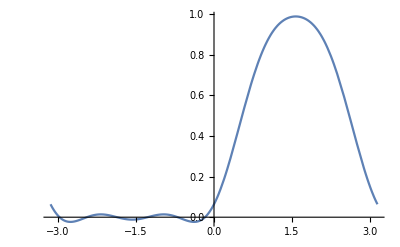

```mathematica
Plot[fourtrig,{x,-π,π}]
```

### P7 .8 .13 Find the complex exponential series for f[x] =2-x -2<x<2 , periodically repeated. Explicitly calculate the integrals that define the coefficients for every exponential term. You can check your answer with the FourierSeries function. Consult the Handbook Fourier series notebook for guidance on how to do this. Use ExpToTrig to show that the complex exponential series is a conventional trigonometric series in disguise. Make a graph of several periods of f[x] and compare your complex exponential series to it. Recall that Mod[x,per,off] is a convenient way to generate periodic behavior.

Defining a variable to represent our function.
We use Mod[] to graph several periods.

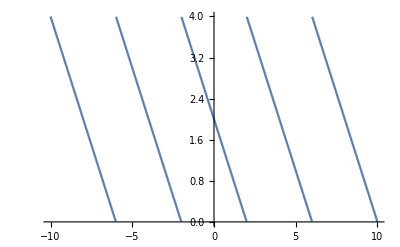

```mathematica
func=2-x;
Plot[2-Mod[x,4,-2],{x,-10,10}]
```

A orthonormal complex exponential basis is given by:

```mathematica
cexp2L[n_]:=ⅇ^(ⅈ (π n x)/L)/Sqrt[2L]
```

We also define a Hermitian inner product to be:

```mathematica
hip2L[f_,g_]:=Integrate[(f/.Complex[x_,y_]->Complex[x,-y])*g,{x,-L,L}]
```

Now that we have our basis and its proper inner product, we can construct our Fourier Series, however
unlike how we usually define the symbolic Fourier Series first and then solve for the coefficients A[n].

In this case, the prompt tells us to adopt complex exponentials as a basis. We can generate the basis functions using
cexp2L[] and also we have to take the Hermitian inner product because complex inner products obey different axioms.

```mathematica
nterms=5
```

5

```mathematica
fourser=Sum[cexp2L[i]*hip2L[cexp2L[i],func],{i,-nterms,nterms}]/.L->2
```

2-(2 ⅈ ⅇ^(-1/2 ⅈ π x))/π+(2 ⅈ ⅇ^((ⅈ π x)/2))/π+(ⅈ ⅇ^(-ⅈ π x))/π-(ⅈ ⅇ^(ⅈ π x))/π-(2 ⅈ ⅇ^(-3/2 ⅈ π x))/(3 π)+(2 ⅈ ⅇ^((3 ⅈ π x)/2))/(3 π)+(ⅈ ⅇ^(-2 ⅈ π x))/(2 π)-(ⅈ ⅇ^(2 ⅈ π x))/(2 π)-(2 ⅈ ⅇ^(-5/2 ⅈ π x))/(5 π)+(2 ⅈ ⅇ^((5 ⅈ π x)/2))/(5 π)

In Trig. form our series looks like:

```mathematica
ExpToTrig[fourser]
```

2-(4 Sin[(π x)/2])/π+(2 Sin[π x])/π-(4 Sin[(3 π x)/2])/(3 π)+Sin[2 π x]/π-(4 Sin[(5 π x)/2])/(5 π)

Plotting our series:

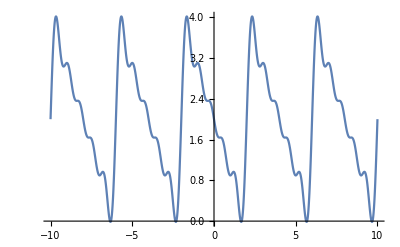

```mathematica
Plot[fourser,{x,-10,10}]
```

Checking our answer with FourierSeries[]:

```mathematica
check=FourierSeries[func,x,nterms,FourierParameters->{1,π/2}]
```

2-(2 ⅈ ⅇ^(-1/2 ⅈ π x))/π+(2 ⅈ ⅇ^((ⅈ π x)/2))/π+(ⅈ ⅇ^(-ⅈ π x))/π-(ⅈ ⅇ^(ⅈ π x))/π-(2 ⅈ ⅇ^(-3/2 ⅈ π x))/(3 π)+(2 ⅈ ⅇ^((3 ⅈ π x)/2))/(3 π)+(ⅈ ⅇ^(-2 ⅈ π x))/(2 π)-(ⅈ ⅇ^(2 ⅈ π x))/(2 π)-(2 ⅈ ⅇ^(-5/2 ⅈ π x))/(5 π)+(2 ⅈ ⅇ^((5 ⅈ π x)/2))/(5 π)

### P7 .9 .23 A violin string is plucked at time t=0 with a deviation from the straight line f(x,0) as shown in the figure. To calculate the subsequent motion f[x,t], the displacement at time t at point x, we will see later that it is first necessary to expand f[x,0] in a Fourier sine series. Find the series if a string of length L is plucked at the center by a height h. Make sure it works by making a plot of the deflection for L->4,h->1.

Plotting our function:

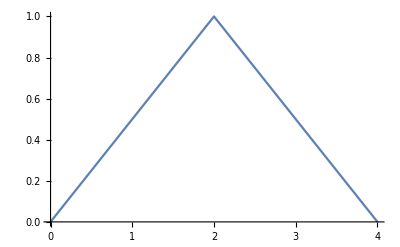

```mathematica
func=Which[0≤x<L/2,h/(L/2)x,x==L/2,h,L/2<x≤L,-h/(L/2)x+2h];
funcplot=Plot[func/.{L->4,h->1},{x,0,4}]
```

Clearly a Sin[] basis would work out perfect in this case, thus we being grinding out our Fourier Series routine:

```mathematica
nterms=10
```

10

```mathematica
fourser=Sum[A[n] Sin[(n π x)/L],{n,1,nterms}]
```

A[1] Sin[(π x)/L]+A[2] Sin[(2 π x)/L]+A[3] Sin[(3 π x)/L]+A[4] Sin[(4 π x)/L]+A[5] Sin[(5 π x)/L]+A[6] Sin[(6 π x)/L]+A[7] Sin[(7 π x)/L]+A[8] Sin[(8 π x)/L]+A[9] Sin[(9 π x)/L]+A[10] Sin[(10 π x)/L]

```mathematica
lhs[n_]:=Integrate[func*Sin[(n π x)/L],{x,0,L},Assumptions->L>0]
rhs[n_]:=Integrate[fourser*Sin[(n π x)/L],{x,0,L},Assumptions->L>0]
```

```mathematica
equations=Table[lhs[i]==rhs[i],{i,1,nterms}]
```

{(4 h L)/π^2==1/2 L A[1],0==1/2 L A[2],-(4 h L)/(9 π^2)==1/2 L A[3],0==1/2 L A[4],(4 h L)/(25 π^2)==1/2 L A[5],0==1/2 L A[6],-(4 h L)/(49 π^2)==1/2 L A[7],0==1/2 L A[8],(4 h L)/(81 π^2)==1/2 L A[9],0==1/2 L A[10]}

```mathematica
Asol=Solve[equations,Table[A[i],{i,1,nterms}]]//Flatten
```

{A[1]→(8 h)/π^2,A[2]→0,A[3]→-(8 h)/(9 π^2),A[4]→0,A[5]→(8 h)/(25 π^2),A[6]→0,A[7]→-(8 h)/(49 π^2),A[8]→0,A[9]→(8 h)/(81 π^2),A[10]→0}

```mathematica
fourser2=fourser/.Asol
```

(8 h Sin[(π x)/L])/π^2-(8 h Sin[(3 π x)/L])/(9 π^2)+(8 h Sin[(5 π x)/L])/(25 π^2)-(8 h Sin[(7 π x)/L])/(49 π^2)+(8 h Sin[(9 π x)/L])/(81 π^2)

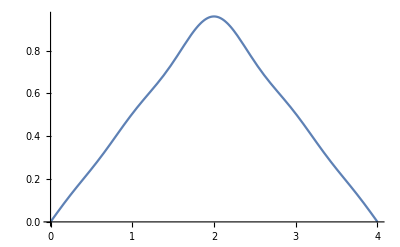

```mathematica
Plot[fourser2/.{L->4,h->1},{x,0,4}]
```

### P7 .12 .9 a) Find the Fourier transform f(k) for the function in the sketch. Make a plot of the Fourier transform as a function of k.

Defining and plotting our function:

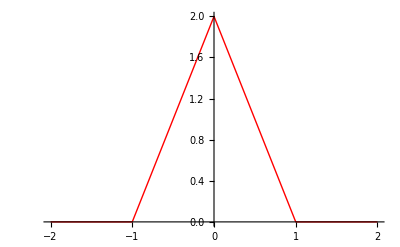

```mathematica
func=Which[x<-a,0,-a<x<0,2 a+2 x,0<x<a,2 a-2 x,x>a,0];
Plot[func/.a->1,{x,-2,2},PlotStyle->{Red,Thick}]
```

From the Mathematica Handbook, we can define a function to conveniently compute a
Fourier Series transformation:

```mathematica
fourtran=Integrate[ⅇ^(ⅈ k x)*func,{x,-∞,∞},Assumptions->a>0]/Sqrt[2π]//Simplify
```

-(√2 ⅇ^(-ⅈ a k) (-1+ⅇ^(ⅈ a k))^2)/(k^2 √π)

In Trig. form our series looks like:

```mathematica
ExpToTrig[fourtran]//Simplify
```

(4 √(2/π) Sin[(a k)/2]^2)/k^2

We can also compute the Fourier Series “by hand”, we would have to break up the region of integration into 2 pieces:

```mathematica
four1=Integrate[ⅇ^(ⅈ k x)*(2a+2x),{x,-a,0},Assumptions->a>0]/Sqrt[2π]
```

(2-2 ⅇ^(-ⅈ a k)-2 ⅈ a k)/(k^2 √(2 π))

```mathematica
four2=Integrate[ⅇ^(ⅈ k x)*(2a-2x),{x,0,a},Assumptions->a>0]/Sqrt[2π]
```

(2-2 ⅇ^(ⅈ a k)+2 ⅈ a k)/(k^2 √(2 π))

```mathematica
fourtran2=four1+four2//Simplify
```

-(√2 ⅇ^(-ⅈ a k) (-1+ⅇ^(ⅈ a k))^2)/(k^2 √π)

In Trig form:

```mathematica
ExpToTrig[fourtran2]
```

-(√(2/π) (Cos[a k]-ⅈ Sin[a k]) (-1+Cos[a k]+ⅈ Sin[a k])^2)/k^2

We can check using FourierTransform[]:

```mathematica
FourierTransform[func,x,k,Assumptions->a>0]
```

-(√2 ⅇ^(-ⅈ a k) (-1+ⅇ^(ⅈ a k))^2)/(k^2 √π)

NOTE: a is our given parameter whereas k is the Fourier Transform pair variable:

### P8 .11 .15 a & d Compute a) ∫_0^π Sin[x] δ(x-π/2)ⅆx and d) ∫_0^π Cosh[x] δ''(x-1)ⅆx . Use basic properties of δ(x) to do the problem “by hand” , and then verify with DiracDelta

```mathematica
nterms=3
```

3

The mechanics of how DiracDelta functions work is that they output 1 when x=x_0 where x_0 is the point of interest, and they output
0 for every other x. 
Because of this behavior, we can just take the Taylor Series approximation around x_0=π/2 for the function Sin[x] particularly.

```mathematica
approx1=Series[Sin[x],{x,π/2,nterms}]//Normal//Simplify
```

1-1/8 (π-2 x)^2

With the point of interesting being x_0=π/2, we should replace x→x_0:

```mathematica
approx1/.x->π/2
```

1

We can check our answer by integrating directly:

```mathematica
Integrate[Sin[x] DiracDelta[x-π/2],{x,0,π}]
```

1

We do a similar approach to finding part (d), however this time since we are given the 2nd derivative of the DiracDelta function
we take the 2nd derivative of our Taylor Series approximation and then sub x → x_0=1:

```mathematica
approx2=Series[Cosh[x],{x,1,nterms}]//Normal//Simplify
```

Cosh[1]+1/2 (-1+x)^2 Cosh[1]+(-1+x) Sinh[1]+1/6 (-1+x)^3 Sinh[1]

```mathematica
approx2=((-1)^n D[approx2,{x,n}])/.n->2
```

Cosh[1]+(-1+x) Sinh[1]

```mathematica
approx2/.x->1
```

```mathematica
Cosh[1]
```

Checking our answer:

```mathematica
Integrate[Cosh[x] D[DiracDelta[x-1],{x,2}],{x,0,π}]
```

Cosh[1]

### P8 .11 .21 a & b Compute a) ∫_0^3 (5x-2) δ(2-x)ⅆx and b) ∫_0^∞ ϕ(x) δ(x^2-a^2)ⅆx Use basic properties of δ(x) and change of variables to do the problem “by hand” , and then verify with DiracDelta

A standard step to doing the problem “by hand” is to take the Taylor Series approximation of our given function
around x_0 and then subbing in the point of interest for x→x_0

```mathematica
nterms=3
```

3

```mathematica
approx1=Series[5x-2,{x,2,nterms}]//Normal//Simplify
```

-2+5 x

```mathematica
approx1/.x->2
```

8

For part (b), we can do a change of variables for the function inside the DiracDelta function: 
∫_0^∞ ϕ(x)δ(x^2-a^2)ⅆx, we let g(x)=x^2-a^2,ⅆg=2xⅆx,x=Sqrt[g+a^2]
Subbing in our variables: 
∫_(-a^2)^∞ ϕ(x)δ(g)ⅆg/(2x)=∫_(-a^2)^∞ ϕ(Sqrt[g+a^2])δ(g)ⅆg/(2Sqrt[g+a^2])
Since the δ function picks out the value of the integrand at the value of the integration variable which makes 
the argument inside the δ function zero (g=0). In this case, it is just x=0, so it’s as if we just plug in zero for g:
∫_(-a^2)^∞ ϕ(Sqrt[g+a^2])δ(g)ⅆg/(2Sqrt[g+a^2])=(ϕ(a))/(2a)

### P8 .3.11 Solve y’ +y Cos[x] = Sin[2 x] Use the standard formula for the first order linear equation y[x]= h[x]+h[x] ∫_0^x h[-w] f[w] dw with h[x]=C_1 ⅇ^(-∫_0^x p[z] dz) and check your result with DSolve.

Defining a variable to represent the given ODE:

```mathematica
eq=y'[x]+y[x] Cos[x]==Sin[2x]
```

Cos[x] y[x]+y'[x]==Sin[2 x]

Before we attempted to define a function to “conveniently” compute h[x] however things got too complicated.
Instead we can straight up plug everything in:

```mathematica
h[x]=ⅇ^(-Integrate[Cos[z],{z,0,x}])
```

ⅇ^(-Sin[x])

```mathematica
sol=C[1]h[x]+h[x]*Integrate[ⅇ^(Sin[w])*Sin[2w],{w,0,x}]//Expand
```

-2+2 ⅇ^(-Sin[x])+ⅇ^(-Sin[x]) C[1]+2 Sin[x]

Checking with DSolve[]:

```mathematica
DSolve[eq,y[x],x]
```

{{y[x]→-2+ⅇ^(-Sin[x]) C[1]+2 Sin[x]}}

### P8 .5 .1 Solve y’’+y’-2y=0 . Do this by explicitly substituting a exponential trial solution using Function to convert the DE to an algebraic equation . Solve the algebraic equation and use the results to construct the general solution of the DE.Use Function to plug in your general solution into the DE to make sure that it works. Check with DSolve.

```mathematica
ClearAll["Global`*"]
```

Defining a variable to represent the given ODE:

```mathematica
eq=y''[x]+y'[x]-2y[x]==0
```

-2 y[x]+y'[x]+y''[x]==0

We employ an exponential trial solution to convert the given ODE into an algebraic equation 
by subbing in y→ⅇ^(r x):

```mathematica
eq2=eq/.y->Function[x,ⅇ^(r x)]
```

-2 ⅇ^(r x)+ⅇ^(r x) r+ⅇ^(r x) r^2==0

```mathematica
eq3=eq2/ⅇ^(r x)//Simplify
```

ⅇ^(-r x) (ⅇ^(r x) (-2+r+r^2)==0)

Simplifying the equation, we can see that the solutions are the roots to the polynomial: r^2+r-2=0:

```mathematica
roots=Solve[-2+r+r^2==0]
```

{{r→-2},{r→1}}

Creating a general solution:

```mathematica
trialsol=ⅇ^(r x)
```

ⅇ^(r x)

```mathematica
homosol=trialsol/.roots
```

{ⅇ^(-2 x),ⅇ^x}

```mathematica
gensol=Thread[{C[1],C[2]}*homosol]//Total
```

ⅇ^(-2 x) C[1]+ⅇ^x C[2]

Testing our trial solutions:

```mathematica
eq/.y->Function[x,ⅇ^(-2x)]
```

True

```mathematica
eq/.y->Function[x,ⅇ^(x)]
```

True

```mathematica
eq/.y->Function[x,ⅇ^(-2 x) C[1]+ⅇ^x C[2]]//Simplify
```

True

Using DSolve[] to check our answer:

```mathematica
DSolve[eq,y[x],x]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^x C[2]}}

```mathematica
Integrate[ⅇ^-x,{x,0,1}]
```

(-1+ⅇ)/ⅇ

```mathematica
Integrate[ⅇ^x,{x,0,1}]
```

-1+ⅇ

```mathematica
(-1+ⅇ)/ⅇ==-1+ⅇ
```

False

```mathematica
Series[Sin[x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Series[1/Sqrt[1+x],{x,0,3}]
```

1-x/2+(3 x^2)/8-(5 x^3)/16+O[x]^4

### P8 .5 .3 Solve y’’+2y’+2y=0 . Do this by explicitly substituting an exponential trial solution using Function to convert the DE to an algebraic equation . Solve the algebraic equation and construct a general two parameter family of solutions of complex exponentials. Find an equivalent two parameter family that is manifestly real ( see Eq. 8.5.16) ; use Function to plug it into the DE to verify. Check with DSolve.

```mathematica
eq=y''[x]+2y'[x]+2y[x]==0
```

2 y[x]+2 y'[x]+y''[x]==0

```mathematica
eq2=eq/.y->Function[x,ⅇ^(r x)]
```

2 ⅇ^(r x)+2 ⅇ^(r x) r+ⅇ^(r x) r^2==0

```mathematica
roots=Solve[eq2,r]
```

{{r→-1-ⅈ},{r→-1+ⅈ}}

```mathematica
trialsol=ⅇ^(r x)/.roots
```

{ⅇ^((-1-ⅈ) x),ⅇ^((-1+ⅈ) x)}

```mathematica
gensolimag=Thread[{C[1],C[2]}*trialsol]//Total
```

ⅇ^((-1-ⅈ) x) C[1]+ⅇ^((-1+ⅈ) x) C[2]

```mathematica
famsol=Function[x,ⅇ^((-1-ⅈ) x) C[1]+ⅇ^((-1+ⅈ) x) C[2]]
```

Function[x,ⅇ^((-1-ⅈ) x) C[1]+ⅇ^((-1+ⅈ) x) C[2]]

```mathematica
eq/.y->famsol//Simplify
```

True

We can use the equation ⅇ^(α x) (C[1] Sin[β x]+C[2] Cos[β x]) to generate a real solution:

```mathematica
gensolreal=ⅇ^(α x)*(C[1]Cos[β x]+C[2] Sin[β x])/.{α->-1,β->1}
```

ⅇ^-x (C[1] Cos[x]+C[2] Sin[x])

```mathematica
eq/.y->Function[x,ⅇ^-x (C[1] Cos[x]+C[2] Sin[x])]//Simplify
```

True

In-Class Activity Week 6:

```mathematica
Series[1/(1-x),{x,0,1}]//Normal
```

1+x

```mathematica
Series[1/(1+x^2),{x,0,2}]//Normal
```

1-x^2

```mathematica
Series[1/(1+ⅇ^-x),{x,0,1}]
```

1/2+x/4+O[x]^2

Week 9 Homework:

-Graphics3D-

```mathematica
func={r(2+Sin[ϕ]^2),r Sin[ϕ] Cos[ϕ],3z}
```

{r (2+Sin[ϕ]^2),r Cos[ϕ] Sin[ϕ],3 z}

For top surface:

```mathematica
Integrate[func.{0,0,1}*r/.z->5,{r,0,2},{ϕ,0,π/2}]//Simplify
```

15 π

For bottom surface:

```mathematica
Integrate[func.{0,0,-1}*r/.z->0,{r,0,2},{ϕ,0,π/2}]
```

0

For curved side:

```mathematica
Integrate[func.{1,0,0}*r/.r->2,{ϕ,0,π/2},{z,0,5}]
```

25 π

For side along x-axis:

```mathematica
Integrate[func.{0,-1,0}*r/.ϕ->0,{r,0,2},{z,0,5}]
```

0

For side along y-axis:

```mathematica
Integrate[func.{0,1,0}*r/.ϕ->π/2,{r,0,2},{z,0,5}]
```

0

```mathematica
Integrate[Div[func,{r,ϕ,z},"Cylindrical"],{r,0,2},{ϕ,0,π/2},{z,0,5}]
```

40 π

```mathematica
nterms=5
```

5

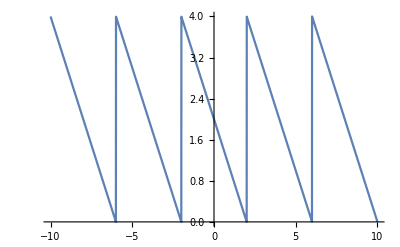

```mathematica
func=2-x;
funcplot=Plot[2-Mod[x,4,-2],{x,-10,10},Exclusions->None]
```

```mathematica
SymbolicFourierSeries=Sum[A[n]ⅇ^(-(π ⅈ n x)/L),{n,-nterms,nterms}]
```

ⅇ^((5 ⅈ π x)/L) A[-5]+ⅇ^((4 ⅈ π x)/L) A[-4]+ⅇ^((3 ⅈ π x)/L) A[-3]+ⅇ^((2 ⅈ π x)/L) A[-2]+ⅇ^((ⅈ π x)/L) A[-1]+A[0]+ⅇ^(-(ⅈ π x)/L) A[1]+ⅇ^(-(2 ⅈ π x)/L) A[2]+ⅇ^(-(3 ⅈ π x)/L) A[3]+ⅇ^(-(4 ⅈ π x)/L) A[4]+ⅇ^(-(5 ⅈ π x)/L) A[5]

```mathematica
lhs[n_]:=Integrate[SymbolicFourierSeries*ⅇ^(-(π ⅈ n x)/L),{x,-L,L}]
rhs[n_]:=Integrate[func*ⅇ^(-(π ⅈ n x)/L),{x,-L,L}]
```

```mathematica
equations=Table[lhs[i]==rhs[i],{i,-nterms,nterms}];
TableForm[equations]
```

2 L A[5]==-(2 ⅈ L^2)/(5 π)
2 L A[4]==(ⅈ L^2)/(2 π)
2 L A[3]==-(2 ⅈ L^2)/(3 π)
2 L A[2]==(ⅈ L^2)/π
2 L A[1]==-(2 ⅈ L^2)/π
2 L A[0]==4 L
2 L A[-1]==(2 ⅈ L^2)/π
2 L A[-2]==-(ⅈ L^2)/π
2 L A[-3]==(2 ⅈ L^2)/(3 π)
2 L A[-4]==-(ⅈ L^2)/(2 π)
2 L A[-5]==(2 ⅈ L^2)/(5 π)

```mathematica
Solve[equations,Table[A[n],{n,-nterms,nterms}]]//Flatten
```

{A[-5]→(ⅈ L)/(5 π),A[-4]→-(ⅈ L)/(4 π),A[-3]→(ⅈ L)/(3 π),A[-2]→-(ⅈ L)/(2 π),A[-1]→(ⅈ L)/π,A[0]→2,A[1]→-(ⅈ L)/π,A[2]→(ⅈ L)/(2 π),A[3]→-(ⅈ L)/(3 π),A[4]→(ⅈ L)/(4 π),A[5]→-(ⅈ L)/(5 π)}

```mathematica
NumericalFourierSeries=SymbolicFourierSeries/.%/.L->2//Simplify
```

(ⅈ ⅇ^(-5/2 ⅈ π x) (-12+15 ⅇ^((ⅈ π x)/2)-20 ⅇ^(ⅈ π x)+30 ⅇ^((3 ⅈ π x)/2)-60 ⅇ^(2 ⅈ π x)+60 ⅇ^(3 ⅈ π x)-30 ⅇ^((7 ⅈ π x)/2)+20 ⅇ^(4 ⅈ π x)-15 ⅇ^((9 ⅈ π x)/2)+12 ⅇ^(5 ⅈ π x)-60 ⅈ ⅇ^((5 ⅈ π x)/2) π))/(30 π)

```mathematica
FourierPlot=Plot[NumericalFourierSeries/.L->2,{x,-10,10},PlotStyle->{Red}];
```

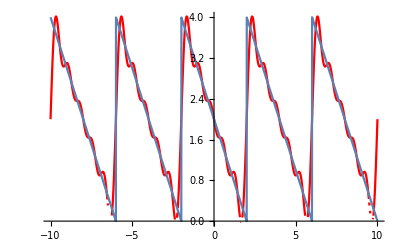

```mathematica
Show[FourierPlot,funcplot]
```

```mathematica
Cosh[0]//N
```

1.

```mathematica
Integrate[Cosh[x] D[DiracDelta[x],x],{x,0,2π}]//N
```

0.

```mathematica
Cosh[0.5]//N
```

1.12763

```mathematica
Integrate[Cosh[x] D[DiracDelta[x-0.5],x],{x,0,2π}]//N
```

-0.521095

```mathematica
Cosh[1]//N
```

1.54308

```mathematica
Integrate[Cosh[x] D[DiracDelta[x-1],x],{x,0,2π}]//N
```

-1.1752

```mathematica
Cosh[π]//N
```

11.592

```mathematica
Integrate[Cosh[x] D[DiracDelta[x-π],x],{x,0,2π}]//N
```

-11.5487

```mathematica
Cosh[3π/2]//N
```

55.6634

```mathematica
Integrate[Cosh[x] D[DiracDelta[x-3π/2],x],{x,0,2π}]//N
```

-55.6544